```mathematica
pathToSolutions=FileNameJoin[{NotebookDirectory[],"dataOut/solutionMatrix.csv"}];
solutions=Import[pathToSolutions,"Table"];
(*pathToEigenvalues=FileNameJoin[{NotebookDirectory[],"dataOut/eigenvalueArray.csv"}];
eigenvalues=Import[pathToEigenvalues,"Table"];*)
```

```mathematica
HarmonicOscillatorψ[n_,x_,m_,ω_,ℏ_]:=((m ω)/(π ℏ))^(1/4)1/(√(2^n n!))HermiteH[n,√((m ω)/ℏ)x] ⅇ^(-(m ω)/(2 ℏ)x^2);
```

```mathematica
Manipulate[
ListLinePlot[solutions[[i]],DataRange->{0,5},PlotRange->Automatic],
{{i,71},1,750,1}
]
```

For N = 750, ρ_max = 5.0

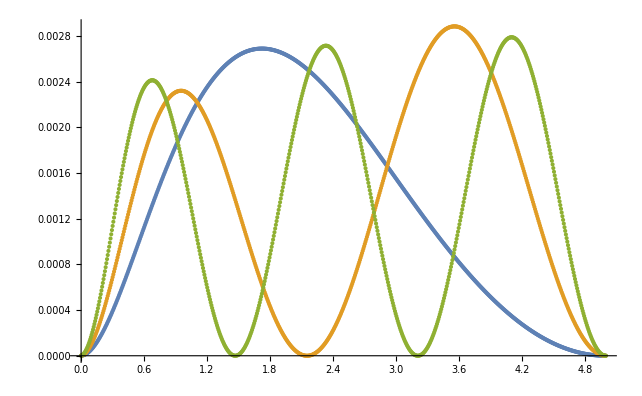

```mathematica
Show[ListPlot[Table[(Transpose[solutions][[263-i]])^2,{i,0,2}],DataRange->{0,5}]]
```

For N = 750, ρ_max = 10.0

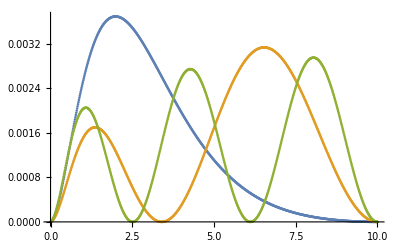

```mathematica
Show[ListPlot[Table[(Transpose[solutions][[258-i]])^2,{i,0,2}],DataRange->{0,10}]]
```

For N = 1000, ρ_max = 10.0

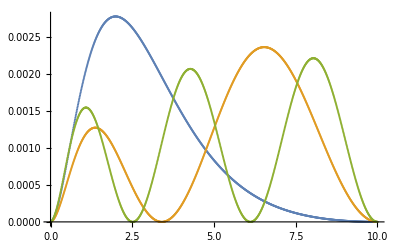

```mathematica
Show[ListPlot[Table[(Transpose[solutions][[348-i]])^2,{i,0,2}],DataRange->{0,10}]]
```